```mathematica
joueur1Img = -Graphics-;
joueur2Img = -Graphics-;
invalidCellImg = -Graphics-;
WinImg= -Graphics-
```

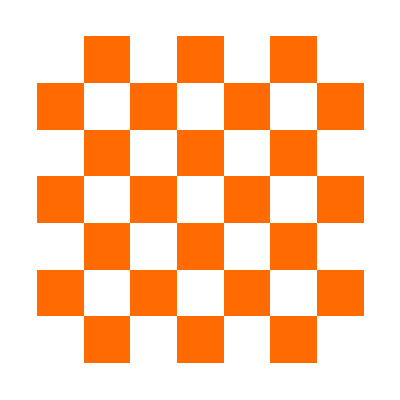

Set::partd: Part specification GridGraphics⟦1⟧ is longer than depth of object.

```mathematica
GridGraphics= cb[n_Integer/;n>0]:=MatrixPlot[SparseArray[{i_,j_}:>Mod[i+j,2],{n,n}],Frame->None]

cb[7]
```

```mathematica
(*Define the two lists of lists*)list1=Table[RandomInteger[100,{5}],{4}];
list2=Table[RandomChoice[{1,Null},{5}],{4}];

(*Create the third list of lists based on the criteria*)
list3=MapThread[MapThread[If[#2===1,#1,Null]&,{#1,#2}]&,{list1,list2}];

(*Display the lists*)
list1
list2
list3
```

{{87,89,62,89,35},{83,96,85,24,57},{6,7,57,74,66},{36,51,88,71,98}}

{{1,Null,Null,Null,Null},{1,1,1,Null,1},{1,1,1,1,1},{Null,1,1,1,1}}

{{87,Null,Null,Null,Null},{83,96,85,Null,57},{6,7,57,74,66},{Null,51,88,71,98}}